## Saturation

```mathematica
S[u_,p_]:=(u/(1+(u)^p)^(1/p));
```

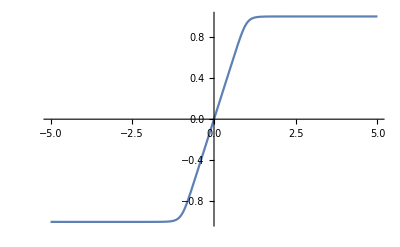

```mathematica
Plot[S[u,10],{u,-5,5}, Axes->Equal]
```

```mathematica
D[S[u,10],u]//Simplify
```

1/((1+u^10)^(11/10))

## Speeds

```mathematica
M = ({{CuT, CuT}, {r CuT, -r CuT}});
{{omegau1},{omegau2}}= Sqrt[Inverse[M].{{T},{tauuz}}]
```

{{√(T/(2 CuT)+tauuz/(2 CuT r))},{√(T/(2 CuT)-tauuz/(2 CuT r))}}

## Derivatives

### calcDesiredRotorSpeeds

```mathematica
ω1s2 = Ts/(2*KT) + τzs/(2*KT*r);
ω2s2 = Ts/(2*KT) - τzs/(2*KT*r);
```

```mathematica
ins = {Ts, τzs, KT, r};
D[ω1s2, {ins}]
D[ω2s2, {ins}]
```

{1/(2 KT),1/(2 KT r),-Ts/(2 KT^2)-τzs/(2 KT^2 r),-τzs/(2 KT r^2)}

{1/(2 KT),-1/(2 KT r),-Ts/(2 KT^2)+τzs/(2 KT^2 r),τzs/(2 KT r^2)}

## Controller Derivatives

```mathematica
Clear[Fxs,Fys]
```

```mathematica
rT[t_]:={{xT[t]},{yT[t]}};
r[t_]:={{x[t]},{y[t]}};
```

```mathematica
θs[t_]:=ArcTan[-Fxs[t]/Fys[t]] - Pi/2
```

```mathematica
θs'[t]//Simplify
```

(-Fys[t] Fxs'[t]+Fxs[t] Fys'[t])/(Fxs[t]^2+Fys[t]^2)

```mathematica
D[θs'[t],{{Fxs[t],Fys[t],Fxs'[t],Fys'[t]}}]/.{Fxs[t]->x,Fys[t]->y,Fxs'[t]->xd,Fys'[t]->yd}//Simplify
```

{(2 x xd y-x^2 yd+y^2 yd)/((x^2+y^2)^2),(-x^2 xd+xd y^2-2 x y yd)/((x^2+y^2)^2),-y/(x^2+y^2),x/(x^2+y^2)}

```mathematica
Fxs[t_]:=-kpr*epx[t]-kdr*evx[t];
Fys[t_]:=-kpr*epy[t] - kdr * evy[t] + m g;
```

```mathematica
Fxs'[t]
```

-kpr epx'[t]-kdr evx'[t]

```mathematica
Fys'[t]
```

-kpr epy'[t]-kdr evy'[t]